```mathematica
(*ML Data*)

(*differences Y Vector*)
Data=Import["G:\\.shortcut-targets-by-id\\17WrugWUn3l1ON6QYmzE0UD-ifioHGbb0\\Priscila\\Research\\USMA\\New Approach\\COOLF1MathematicaReads.xlsx];
ΔYVec=Data[[1,All,2]];

nΔYVec=Length[ΔYVec]
```

```mathematica
(*the whole Y Vec*)
YVec=Data[[1,All,1]];
n=Length[YVec]
```

84

```mathematica
(*fitting to 90% of the data*)
n90=Floor[nΔYVec (0.9)]
```

75

```mathematica
(*Covariates*)


(*Yield Curve*)
X1Vec=Data[[1,All,3]];

(*Norfarm Jobs*)
X2Vec=Data[[1,All,4]];

(*Federal Funds*)
X3Vec=Data[[1,All,5]];

(*Mortgage Rate*)
X4Vec=Data[[1,All,6]];

(*Personal Consumption Expeditures*)
X5Vec=Data[[1,All,7]];

(*Industrial Production*)
X6Vec=Data[[1,All,8]];

(*Consumer Price Index*)
X7Vec=Data[[1,All,9]];

(*Crude Oil Prices*)
X8Vec=Data[[1,All,10]];

(*NASDAQ Composite Index*)
X9Vec=Data[[1,All,11]];
```

```mathematica
(*Plot Y - Observed data*)
```

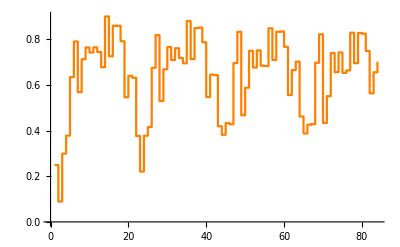

```mathematica
x=Table[i,{i,1,n}];
dataPlot=Transpose[{x,YVec}];
YObserved=ListPlot[dataPlot,InterpolationOrder->0, Joined->True,PlotRange->All,PlotStyle->Orange]
```

```mathematica
(* MLR*)
```

```mathematica
(*Normal Distribution*)
L=1/((2 π σ^2)^(n90/2))Exp[-1/(2 σ^2) (∑_(i=3)^n90 ((ΔYVec[[i]]-(β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β4 X4[[i]]+β7 X1[[i]] X2[[i]] + β8 X1[[i]] X3[[i]]+β9 X1[[i]] X4[[i]] +β12 X2[[i]] X3[[i]] +β13 X2[[i]] X4[[i]] +β16 X3[[i]] X4[[i]] +β21 YVec[[i-1]] +β22 X1[[i-1]]+β23 X2[[i-1]]+β24 X3[[i-1]]+β25 X4[[i-1]] +β28 YVec[[i-2]] +β29 X1[[i-2]]+β30 X2[[i-2]]+β31 X3[[i-2]]+β32 X4[[i-2]] ))/.{X1->    X8Vec,X2-> X2Vec,X3->X3Vec,X4->X4Vec})^2)];
LnL=Log[L];


Dβ0=Simplify[D[LnL,β0]];
Dβ1=Simplify[D[LnL,β1]];
Dβ2=Simplify[D[LnL,β2]];
Dβ3=Simplify[D[LnL,β3]];
Dβ4=Simplify[D[LnL,β4]];


Dβ7=Simplify[D[LnL,β7]];
Dβ8=Simplify[D[LnL,β8]];
Dβ9=Simplify[D[LnL,β9]];


Dβ12=Simplify[D[LnL,β12]];
Dβ13=Simplify[D[LnL,β13]];

Dβ16=Simplify[D[LnL,β16]];




Dβ21=Simplify[D[LnL,β21]];
Dβ22=Simplify[D[LnL,β22]];
Dβ23=Simplify[D[LnL,β23]];
Dβ24=Simplify[D[LnL,β24]];
Dβ25=Simplify[D[LnL,β25]];


Dβ28=Simplify[D[LnL,β28]];
Dβ29=Simplify[D[LnL,β29]];
Dβ30=Simplify[D[LnL,β30]];
Dβ31=Simplify[D[LnL,β31]];
Dβ32=Simplify[D[LnL,β32]];


Dσ=Simplify[D[LnL,σ]];

RulesInt=FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ7},{0==Dβ8},{0==Dβ9},{0==Dβ12},{0==Dβ13},{0==Dβ16},{0==Dβ21},{0==Dβ22},{0==Dβ23},{0==Dβ24},{0==Dβ25},{0==Dβ28},{0==Dβ29},{0==Dβ30},{0==Dβ31},{0==Dβ32},{0==Dσ}},{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β7,0.1},{β8,0.1},{β9,0.1},{β12,0.1},{β13,0.1},{β16,0.1},{β21,0.1},{β22,0.1},{β23,0.1},{β24,0.1},{β25,0.1},{β28,0.1},{β29,0.1},{β30,0.1},{β31,0.1},{β32,0.1},{σ,0.1}, MaxIterations->1000]//Quiet
```

Part::partd: Part specification X1⟦3⟧ is longer than depth of object.

Part::partd: Part specification X2⟦3⟧ is longer than depth of object.

Part::partd: Part specification X3⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{β0→-1531.19,β1→15.2379,β2→0.761544,β3→-0.487387,β4→0.233508,β7→0.0248006,β8→-0.0823654,β9→-0.0023147,β12→-0.000173287,β13→-0.0004481,β16→0.0011935,β21→-0.740459,β22→-0.00156729,β23→-0.145956,β24→0.43753,β25→-0.000334777,β28→0.251573,β29→-0.0378244,β30→-0.0177053,β31→0.0506212,β32→-0.00012751,σ→7.46057×10^102}

```mathematica
(*Prediction*)
LRInt=β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β4 X4[[i]]+β7 X1[[i]] X2[[i]] + β8 X1[[i]] X3[[i]]+β9 X1[[i]] X4[[i]] +β12 X2[[i]] X3[[i]] +β13 X2[[i]] X4[[i]] +β16 X3[[i]] X4[[i]] +β21 YVec[[i-1]] +β22 X1[[i-1]]+β23 X2[[i-1]]+β24 X3[[i-1]]+β25 X4[[i-1]]+ β28 YVec[[i-2]] +β29 X1[[i-2]]+β30 X2[[i-2]]+β31 X3[[i-2]]+β32 X4[[i-2]];
LRInt=LRInt/.RulesInt; 

YFitListInt=.
YFitListInt={ΔYVec[[1]],ΔYVec[[2]]};
For[k=3,k<=nΔYVec,
AppendTo[YFitListInt,LRInt/.{X1->    X8Vec,X2-> X2Vec,X3->X3Vec,X4->X4Vec,i->k}]//Quiet;
k=k+1;
];
YFitListInt
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression -2+i cannot be used as a part specification.

Part::pkspec1: The expression -1+i cannot be used as a part specification.

{0.,-0.159757,0.215713,0.0456493,0.267217,0.162577,-0.307743,0.0732793,0.0809792,-0.0289388,-0.00676474,-0.0327545,-0.0506886,0.203812,-0.180168,0.130101,-0.00544655,-0.0716251,-0.236547,0.10553,0.0153231,-0.222153,-0.0641936,0.150455,0.0208032,0.259017,0.141558,-0.318107,0.108965,0.104051,-0.0412933,0.0179276,-0.03813,-0.0320948,0.184376,-0.161096,0.134309,-0.000938331,-0.0681598,-0.235283,0.103371,0.011648,-0.229332,-0.0930373,0.0419692,0.0201376,0.264069,0.129544,-0.323575,0.158882,0.147973,-0.0494882,0.0384076,-0.0392888,-0.00956264,0.184933,-0.140438,0.129023,0.0101173,-0.0596856,-0.224728,0.0919948,-0.00077789,-0.267944,-0.10977,0.048416,0.0269191,0.261942,0.128529,-0.315054,0.180896,0.167078,-0.0516893,0.0508964,-0.0379379,0.011692,0.1911,-0.130907,0.134396,0.0106979,-0.0538645,-0.213678,0.0820005,0.00816788}

```mathematica
YFitCumulativeInt=.
YFitCumulativeInt={YVec[[1]]+YFitListInt[[1]]};
For[k=1,k<(nΔYVec),
AppendTo[YFitCumulativeInt,(YFitCumulativeInt[[k]]+YFitListInt[[k+1]])]//Quiet;
k=k+1;
];
YFitCumulativeInt
```

{0.249077,0.0893193,0.305032,0.350682,0.617899,0.780476,0.472733,0.546012,0.626991,0.598052,0.591287,0.558533,0.507844,0.711656,0.531488,0.661589,0.656142,0.584517,0.34797,0.453501,0.468824,0.24667,0.182477,0.332932,0.353735,0.612752,0.75431,0.436203,0.545169,0.64922,0.607927,0.625854,0.587724,0.55563,0.740006,0.57891,0.713218,0.71228,0.64412,0.408837,0.512208,0.523856,0.294524,0.201487,0.243456,0.263594,0.527663,0.657206,0.333631,0.492513,0.640487,0.590998,0.629406,0.590117,0.580555,0.765488,0.62505,0.754073,0.76419,0.704505,0.479777,0.571772,0.570994,0.30305,0.19328,0.241696,0.268615,0.530557,0.659087,0.344032,0.524928,0.692006,0.640317,0.691214,0.653276,0.664968,0.856068,0.725161,0.859557,0.870254,0.81639,0.602712,0.684712,0.69288}

```mathematica
failureCount = Table[index,{index,1,n}];
NewPlot=Transpose[{failureCount,YFitCumulativeInt}]
```

{{1,0.249077},{2,0.0893193},{3,0.305032},{4,0.350682},{5,0.617899},{6,0.780476},{7,0.472733},{8,0.546012},{9,0.626991},{10,0.598052},{11,0.591287},{12,0.558533},{13,0.507844},{14,0.711656},{15,0.531488},{16,0.661589},{17,0.656142},{18,0.584517},{19,0.34797},{20,0.453501},{21,0.468824},{22,0.24667},{23,0.182477},{24,0.332932},{25,0.353735},{26,0.612752},{27,0.75431},{28,0.436203},{29,0.545169},{30,0.64922},{31,0.607927},{32,0.625854},{33,0.587724},{34,0.55563},{35,0.740006},{36,0.57891},{37,0.713218},{38,0.71228},{39,0.64412},{40,0.408837},{41,0.512208},{42,0.523856},{43,0.294524},{44,0.201487},{45,0.243456},{46,0.263594},{47,0.527663},{48,0.657206},{49,0.333631},{50,0.492513},{51,0.640487},{52,0.590998},{53,0.629406},{54,0.590117},{55,0.580555},{56,0.765488},{57,0.62505},{58,0.754073},{59,0.76419},{60,0.704505},{61,0.479777},{62,0.571772},{63,0.570994},{64,0.30305},{65,0.19328},{66,0.241696},{67,0.268615},{68,0.530557},{69,0.659087},{70,0.344032},{71,0.524928},{72,0.692006},{73,0.640317},{74,0.691214},{75,0.653276},{76,0.664968},{77,0.856068},{78,0.725161},{79,0.859557},{80,0.870254},{81,0.81639},{82,0.602712},{83,0.684712},{84,0.69288}}

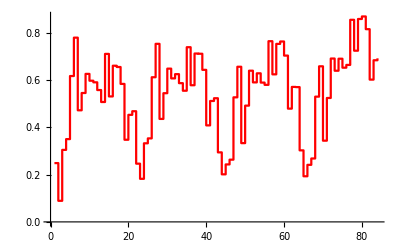

```mathematica
YPredictedPlotInt=ListPlot[(NewPlot),InterpolationOrder->0, Joined->True,PlotStyle->Red,PlotRange->All]
```

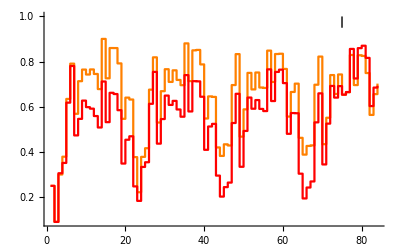

```mathematica
(*Comparing Y observed vs Y predicted with multiple linear regression*)

A=Show[{YObserved,YPredictedPlotInt},Graphics[{Black, Line[{{n90,0.95},{n90,1}}]}],PlotRange->All]
```

```mathematica
(*Measure of the quality of the fit (page 60) *)

(*Prediction of Y using X*)
```

```mathematica
(*SSE*)
```

```mathematica
(*SSE=∑_(i=1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
SSE=∑_(i=1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

1.26816

```mathematica
(*PSSE*)
```

```mathematica
(*PSSE=∑_(i=n90+1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
PSSE=∑_(i=n90+1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.0116018

```mathematica
(*variance*)
```

```mathematica
S2=1/(n-2)(SSE);
```

```mathematica
(*Mean Squared Error*)
MSE=SSE/n;
```

```mathematica
(*Mean Squared Error Predicte data*)
MSEP=PSSE/(n-n90+1)
```

0.00116018

```mathematica
(*Correlation Coefficient*)
```

```mathematica
(*prediction of Y if X is ignored*)
```

```mathematica
SSY=∑_(i=1)^nΔYVec (ΔYVec[[i]]-Mean[ΔYVec])^2;
```

```mathematica
(*values between 0 and 1. The larger the value of r2, the stronger the linear regression between X and Y*)
```

```mathematica
r2=(SSY-SSE)/SSY;
```

```mathematica
(*p is the number of independent variables in the model (excluding the constant term)*)
```

```mathematica
r2Adj=1-(1-r2)(n-1)/(n-p-1)/.p->6
```

0.25639